```mathematica
(*basic set up *)
rightHandSides = { 
	u*f*(N-n) - s*n,
	 γ*n-a*p - δ*p,
	 a*p-λ*c - (r*f)*c,
	 e*r*f*c- m*f*(1+d*f)
};
vars = {n, p, f, c};
equilibria = Solve[0 == rightHandSides, vars, NonNegativeReals]; 
defaultpars = {N-> 10, γ -> 0.1, a -> 0.04, s -> 0.1, u-> .2, δ -> 0.01, λ -> 0.005, e -> 0.01, m->  0.005, r-> 0.8, d-> 0.005};
```

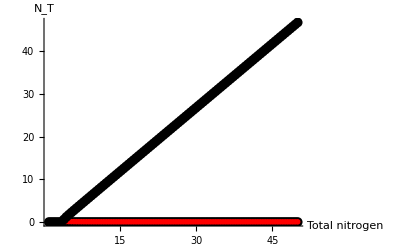

```mathematica
g[x_] := equilibria/.ReplacePart[defaultpars, 1 -> N -> x];  (* last input chooses which parameter we vary in the bifurcation plot *) 

xdata = Subdivide[1, 50, 100];  (* range of values to use*) 
resultTable = Table[g[x], {x, xdata}];
ydata = Table[p/.resultTable[[i]], {i, 1, Length[xdata]}];
ydatapair1 = Transpose[{xdata, ydata[[All, 1]]}];
ydatapair2 = Transpose[{xdata, ydata[[All, 2]]}];
ydatapair3 = Transpose[{xdata, ydata[[All, 3]]}];
plot1=ListPlot[ydatapair1,PlotStyle->Black,PlotMarkers->{Automatic, 10}];
plot2=ListPlot[ydatapair2,PlotStyle->Red,PlotMarkers-> {"OpenMarkers", 4}];
plot3=ListPlot[ydatapair3,PlotStyle->Black,PlotMarkers->{Automatic, 10}];

Show[plot1,plot2,plot3,PlotLegends->{"y1","y2","y3"},AxesLabel->{"Total nitrogen",C_p},PlotRange->Automatic]

(*Start with Uptake*)
```

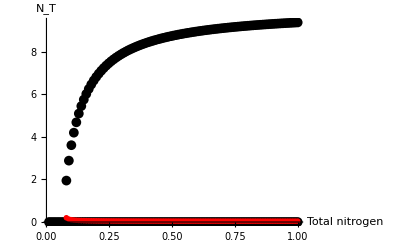

```mathematica
g[x_] := equilibria/.ReplacePart[defaultpars, 5 -> u -> x];  

xdata = Subdivide[0.01, 1, 100];  (* range of values to use*) 
resultTable = Table[g[x], {x, xdata}];
ydata = Table[p/.resultTable[[i]], {i, 1, Length[xdata]}];
ydatapair1 = Transpose[{xdata, ydata[[All, 1]]}];
ydatapair2 = Transpose[{xdata, ydata[[All, 2]]}];
ydatapair3 = Transpose[{xdata, ydata[[All, 3]]}];
plot4=ListPlot[ydatapair1,PlotStyle->Black,PlotMarkers->{Automatic, 10}];
plot5=ListPlot[ydatapair2,PlotStyle->Red,PlotMarkers-> {"OpenMarkers", 4}];
plot6=ListPlot[ydatapair3,PlotStyle->Black,PlotMarkers->{Automatic, 10}];

Show[plot4,plot5,plot6,PlotLegends->{"y1","y2","y3"},AxesLabel->{"Total nitrogen",C_p},PlotRange->Automatic]
```

```mathematica
(* can change axis label to reflext paramter we vary*)
```

```mathematica
g[x_] := equilibria/.ReplacePart[defaultpars, 2 -> γ -> x];  (* last input chooses which parameter we vary in the bifurcation plot *) 

xdata = Subdivide[0, .2, 100];  (* range of values to use*) 
resultTable = Table[g[x], {x, xdata}];
ydata = Table[p/.resultTable[[i]], {i, 1, Length[xdata]}];
ydatapair1 = Transpose[{xdata, ydata[[All, 1]]}];
ydatapair2 = Transpose[{xdata, ydata[[All, 2]]}];
ydatapair3 = Transpose[{xdata, ydata[[All, 3]]}];
plot7=ListPlot[ydatapair1,PlotStyle->Black,PlotMarkers->{Automatic, 10}];
plot8=ListPlot[ydatapair2,PlotStyle->Red,PlotMarkers-> {"OpenMarkers", 4}];
plot9=ListPlot[ydatapair3,PlotStyle->Black,PlotMarkers->{Automatic, 10}];


 (* can change axis label to reflext paramter we vary*)
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

```mathematica
g[x_] := equilibria/.ReplacePart[defaultpars, 3 -> a -> x];  (* last input chooses which parameter we vary in the bifurcation plot *) 

xdata = Subdivide[0, .2, 100];  (* range of values to use*) 
resultTable = Table[g[x], {x, xdata}];
ydata = Table[p/.resultTable[[i]], {i, 1, Length[xdata]}];
ydatapair1 = Transpose[{xdata, ydata[[All, 1]]}];
ydatapair2 = Transpose[{xdata, ydata[[All, 2]]}];
ydatapair3 = Transpose[{xdata, ydata[[All, 3]]}];
plot10=ListPlot[ydatapair1,PlotStyle->Black,PlotMarkers->{Automatic, 10}];
plot11=ListPlot[ydatapair2,PlotStyle->Red,PlotMarkers-> {"OpenMarkers", 4}];
plot12=ListPlot[ydatapair3,PlotStyle->Black,PlotMarkers->{Automatic, 10}];
(* can change axis label to reflext paramter we vary*)
```

```mathematica
g[x_] := equilibria/.ReplacePart[defaultpars, 4 -> s -> x];  (* last input chooses which parameter we vary in the bifurcation plot *) 

xdata = Subdivide[0.001, .5, 100];  (* range of values to use*) 
resultTable = Table[g[x], {x, xdata}];
ydata = Table[p/.resultTable[[i]], {i, 1, Length[xdata]}];
ydatapair1 = Transpose[{xdata, ydata[[All, 1]]}];
ydatapair2 = Transpose[{xdata, ydata[[All, 2]]}];
ydatapair3 = Transpose[{xdata, ydata[[All, 3]]}];
plot13=ListPlot[ydatapair1,PlotStyle->Black,PlotMarkers->{Automatic, 10}];
plot14=ListPlot[ydatapair2,PlotStyle->Red,PlotMarkers-> {"OpenMarkers", 4}];
plot15=ListPlot[ydatapair3,PlotStyle->Black,PlotMarkers->{Automatic, 10}];
(* can change axis label to reflext paramter we vary*)
```

```mathematica
g[x_] := equilibria/.ReplacePart[defaultpars, 6 -> δ -> x];  (* last input chooses which parameter we vary in the bifurcation plot *) xdata = Subdivide[0.001, .2, 100];  (* range of values to use*) 
resultTable = Table[g[x], {x, xdata}];
ydata = Table[p/.resultTable[[i]], {i, 1, Length[xdata]}];
ydatapair1 = Transpose[{xdata, ydata[[All, 1]]}];
ydatapair2 = Transpose[{xdata, ydata[[All, 2]]}];
ydatapair3 = Transpose[{xdata, ydata[[All, 3]]}];
plot16=ListPlot[ydatapair1,PlotStyle->Black,PlotMarkers->{Automatic, 10}];
plot17=ListPlot[ydatapair2,PlotStyle->Red,PlotMarkers-> {"OpenMarkers", 4}];
plot18=ListPlot[ydatapair3,PlotStyle->Black,PlotMarkers->{Automatic, 10}];
(* can change axis label to reflext paramter we vary*)
```

```mathematica
g[x_] := equilibria/.ReplacePart[defaultpars, 7 -> λ -> x];  (* last input chooses which parameter we vary in the bifurcation plot *) xdata = Subdivide[0.001, .5, 100];  (* range of values to use*) 
resultTable = Table[g[x], {x, xdata}];
ydata = Table[p/.resultTable[[i]], {i, 1, Length[xdata]}];
ydatapair1 = Transpose[{xdata, ydata[[All, 1]]}];
ydatapair2 = Transpose[{xdata, ydata[[All, 2]]}];
ydatapair3 = Transpose[{xdata, ydata[[All, 3]]}];
plot19=ListPlot[ydatapair1,PlotStyle->Black,PlotMarkers->{Automatic, 10}];
plot20=ListPlot[ydatapair2,PlotStyle->Red,PlotMarkers-> {"OpenMarkers", 4}];
plot21=ListPlot[ydatapair3,PlotStyle->Black,PlotMarkers->{Automatic, 10}];
```

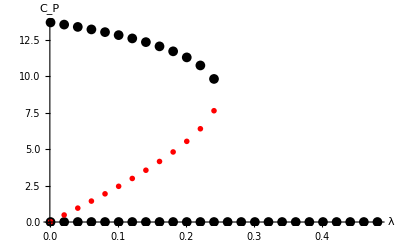

-Graphics-

```mathematica
g[x_] := equilibria/.ReplacePart[defaultpars, 8 -> e -> x];  (* last input chooses which parameter we vary in the bifurcation plot *) xdata = Subdivide[0.001, .1,100];  (* range of values to use*) 
resultTable = Table[g[x], {x, xdata}];
ydata = Table[p/.resultTable[[i]], {i, 1, Length[xdata]}];
ydatapair1 = Transpose[{xdata, ydata[[All, 1]]}];
ydatapair2 = Transpose[{xdata, ydata[[All, 2]]}];
ydatapair3 = Transpose[{xdata, ydata[[All, 3]]}];
plot22=ListPlot[ydatapair1,PlotStyle->Black,PlotMarkers->{Automatic, 10}];
plot23=ListPlot[ydatapair2,PlotStyle->Red,PlotMarkers-> {"OpenMarkers", 4}];
plot24=ListPlot[ydatapair3,PlotStyle->Black,PlotMarkers->{Automatic, 10}];
(* can change axis label to reflext paramter we vary*)
```

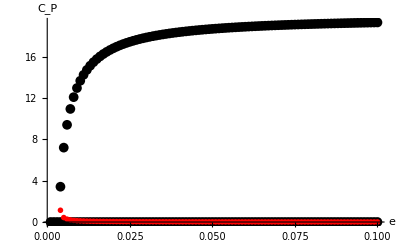

-Graphics-

```mathematica
g[x_] := equilibria/.ReplacePart[defaultpars, 9 -> m -> x];  (* last input chooses which parameter we vary in the bifurcation plot *) xdata = Subdivide[0.001, .05, 100];  (* range of values to use*) 
resultTable = Table[g[x], {x, xdata}];
ydata = Table[p/.resultTable[[i]], {i, 1, Length[xdata]}];
ydatapair1 = Transpose[{xdata, ydata[[All, 1]]}];
ydatapair2 = Transpose[{xdata, ydata[[All, 2]]}];
ydatapair3 = Transpose[{xdata, ydata[[All, 3]]}];
plot25=ListPlot[ydatapair1,PlotStyle->Black,PlotMarkers->{Automatic, 10}];
plot26=ListPlot[ydatapair2,PlotStyle->Red,PlotMarkers-> {"OpenMarkers", 4}];
plot27=ListPlot[ydatapair3,PlotStyle->Black,PlotMarkers->{Automatic, 10}];
(* can change axis label to reflext paramter we vary*)
```

```mathematica
g[x_] := equilibria/.ReplacePart[defaultpars, 10 -> r-> x];  (* last input chooses which parameter we vary in the bifurcation plot *) xdata = Subdivide[0.001, .2, 100];  (* range of values to use*) 
resultTable = Table[g[x], {x, xdata}];
ydata = Table[p/.resultTable[[i]], {i, 1, Length[xdata]}];
ydatapair1 = Transpose[{xdata, ydata[[All, 1]]}];
ydatapair2 = Transpose[{xdata, ydata[[All, 2]]}];
ydatapair3 = Transpose[{xdata, ydata[[All, 3]]}];
plot28=ListPlot[ydatapair1,PlotStyle->Black,PlotMarkers->{Automatic, 10}];
plot29=ListPlot[ydatapair2,PlotStyle->Red,PlotMarkers-> {"OpenMarkers", 4}];
plot30=ListPlot[ydatapair3,PlotStyle->Black,PlotMarkers->{Automatic, 10}];
(* can change axis label to reflext paramter we vary*)
```

```mathematica
g[x_] := equilibria/.ReplacePart[defaultpars, 11-> d-> x];  (* last input chooses which parameter we vary in the bifurcation plot *) 

xdata = Subdivide[0.01, 130, 100];  (* range of values to use*) 
resultTable = Table[g[x], {x, xdata}];
ydata = Table[p/.resultTable[[i]], {i, 1, Length[xdata]}];
ydatapair1 = Transpose[{xdata, ydata[[All, 1]]}];
ydatapair2 = Transpose[{xdata, ydata[[All, 2]]}];
ydatapair3 = Transpose[{xdata, ydata[[All, 3]]}];
plot31=ListPlot[ydatapair1,PlotStyle->Black,PlotMarkers->{Automatic, 10}];
plot32=ListPlot[ydatapair2,PlotStyle->Red,PlotMarkers-> {"OpenMarkers", 4}];
plot33=ListPlot[ydatapair3,PlotStyle->Black,PlotMarkers->{Automatic, 10}];
(* can change axis label to reflext paramter we vary*)
```

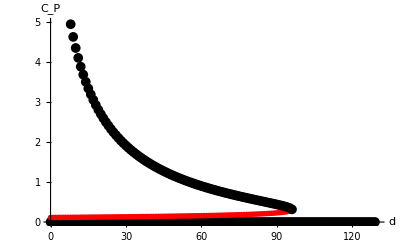

-Graphics-

```mathematica
Panel1 = Show[plot4,plot5,plot6,AxesLabel->{Style["ū",FontSize->20],Style["C_p",FontSize->20]}, TicksStyle->Directive[FontSize->20],PlotRange->Automatic];Panel5 =Show[plot7,plot8,plot9,AxesLabel->{Style["g",FontSize->20],Style["C_p",FontSize->20]}, TicksStyle->Directive[FontSize->20],PlotRange->Automatic];
Panel3 = Show[plot10,plot11,plot12,AxesLabel->{Style["a",FontSize->20],Style["C_p",FontSize->20]}, TicksStyle->Directive[FontSize->20],PlotRange->{{0,0.2},{0,25}}];Panel4 = Show[plot13,plot14,plot15,AxesLabel->{Style["s",FontSize->20],Style["C_p",FontSize->20]}, TicksStyle->Directive[FontSize->20],PlotRange->{{0,0.5},{0,25}}];Panel2= Show[plot16,plot17,plot18,AxesLabel->{Style["δ",FontSize->20],Style["C_P",FontSize->20]}, TicksStyle->Directive[FontSize->20], PlotRange->{{0,0.2},{0,5}}];Panel6 = Show[plot19,plot20,plot21,AxesLabel->{Style["λ",FontSize->20],Style["C_p",FontSize->20]}, TicksStyle->Directive[FontSize->20],PlotRange->Automatic]; 
Panel7 = Show[plot22,plot23,plot24,AxesLabel->{Style["e",FontSize->20],Style["C_p",FontSize->20]}, TicksStyle->Directive[FontSize->20], PlotRange->Automatic];Panel8 = Show[plot25,plot26,plot27,AxesLabel->{Style["m",FontSize->20],Style["C_p",FontSize->20]}, TicksStyle->Directive[FontSize->20], PlotRange->{{0,0.05},{0,16}}];Panel9 =Show[plot28,plot29,plot30,AxesLabel->{Style["r",FontSize->20],Style["C_p",FontSize->20]}, TicksStyle->Directive[FontSize->20], PlotRange->{{0,0.2},{0,16}}];Panel10 =Show[plot31,plot32,plot33,AxesLabel->{Style["d",FontSize->20],Style["C_p",FontSize->20]}, TicksStyle->Directive[FontSize->20],PlotRange->{{0,130},{0,5}}];
```

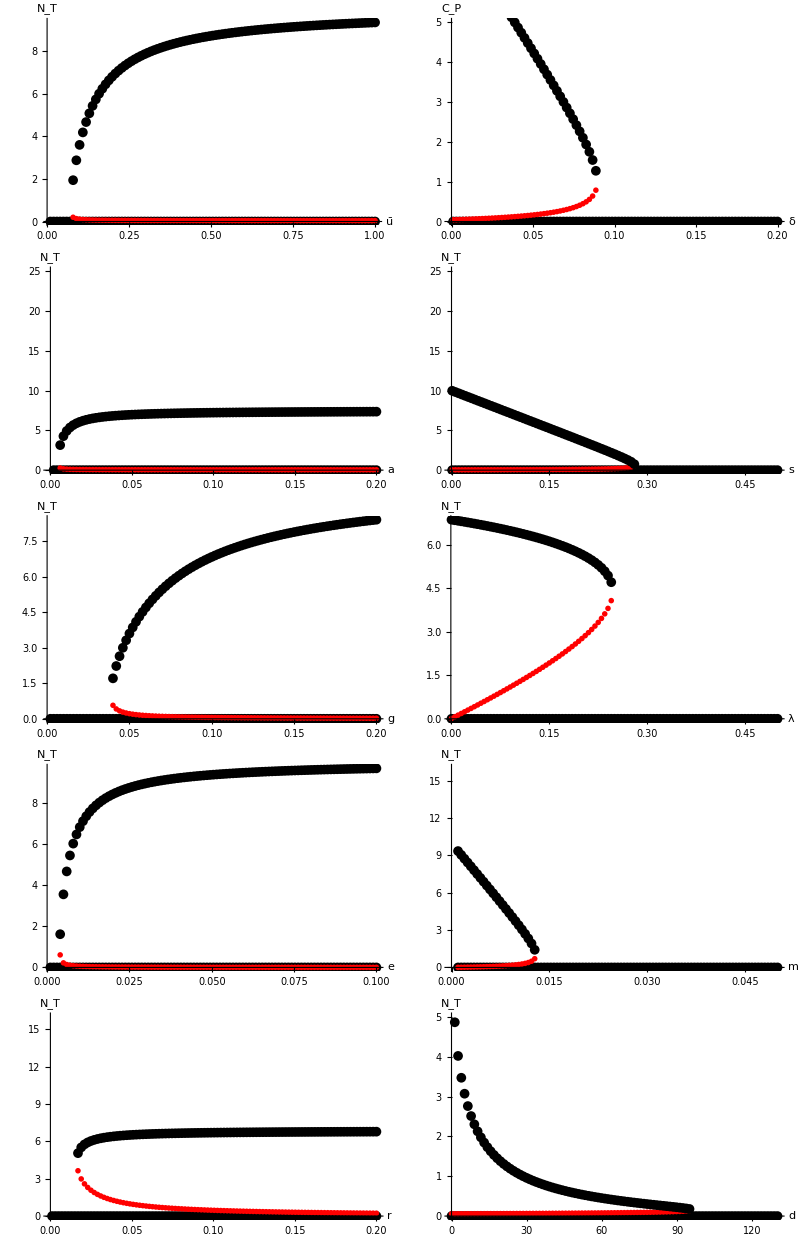

```mathematica
GraphicsGrid[{{Panel1, Panel2}, {Panel3, Panel4}, {Panel5, Panel6}, {Panel7, Panel8},{Panel9, Panel10}},(*Partition into rows of 5 plots each*)Spacings->{2,2} (*Adjust spacing between the plots*)]
```